$Aborted

{1-137.596 timePre[1,1,{0,0,-214},2,-0.5],1-137.596 timePre[1,1,{0,0,-214},2,-0.5],-89.0554 timePre[1,1,{0,0,-214},2,-0.5]-193.11 timePre[1,1,{0,0,-214},2,-0.5]^2}

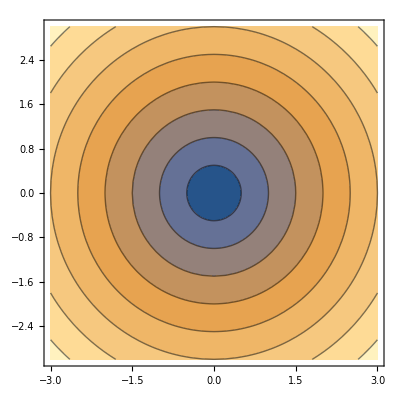

```mathematica
v = {vx,vy,vz};
r = {x,y,0};
p = 1;
θ[x_,y_]:=ArcTan[x,y];
ϕ[x_,y_,d_,k_]:=k Sqrt[x^2+y^2]^d;
u[x_,y_,d_,k_]:=With[{phi = ϕ[x,y,d,k], theta =θ[x,y]},{Cos[theta]Sin[phi],Sin[theta]Sin[phi],Cos[phi]}]
parab[x_,y_,v_]:={x,y,0}+t*v+1/2*t^2*{0,0,-386.2205};
bounceV[u_,v_]:=-u*v.u+(v-u*v.u);
parab[x_,y_,v_,d_,k_]:=parab[x,y,bounceV[u[x,y,d,k],v]]
time[x_,y_,v_,d_,k_]:=Solve[parab[x,y,v,d,k][[3]]==0&&t>0,t][[1]]

pos[x_,y_,v_,d_,k_]:=Evaluate[parab[x,y,v,d,k]/.time[x,y,v,d,k]]
pos[1,1,{0,0,-214},2,-0.5]
dist[x_,y_,v_,k_]:=Norm[pos[x,y,v,k]]
```